# Modeling Infections Diseases in Mathematica Using Cellular Automata

## Disease Modeling using the "Game of Life"

### Introduction

A cellular automaton is a model that simulates a collection of “cells” that live on a grid, in discrete time. Each cell has a state, and a neighborhood of surrounding cells. Here is an example of a 12-by-12 cellular automaton where each cell is randomly set to a value between one and zero:

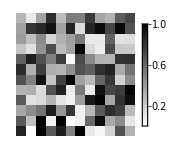

```mathematica
ArrayPlot[RandomReal[1,{12,12}],ImageSize->150,PlotLegends->Automatic]
```

These cells live their entire lives on this grid and can respond to their neighbors. One of the best-known examples of cellular automata is Conway’s Game of Life, which we’ll adapt to model the spread of an infectious disease in Mathematica. In the Game of Life, cells can reproduce, and they can die of overcrowding. Simulating the Game of Life for a long time produces unpredictable and intricate patterns.

In fact, the guy who created Mathematica, Steven Wolfram, is himself a pioneer in the field of cellular automata. His text, A New Kind of Science, is freely available online. Naturally, Mathematica provides a bunch of functions for dealing with cellular automata, most of which (sadly) are too complicated to quickly understand.

In our disease modeling example, a cell's state represents its susceptibility to disease. In the SIR model, cells can be susceptible, infectious, or recovered. We'll actually use a modified model, SLIR, where cells can also be latent (that is, infected but not infectious). This is the same model we used to study HIV earlier in the course.

A cell’s neighborhood is the set of nearby cells that influence the cell. Two neighborhoods are common in cellular automata: the von Neumann neighborhood, which includes the 4 adjacent cells; and the Moore neighborhood, which includes the 8 adjacent cells and diagonals.

```mathematica
Row[{
ArrayPlot[{{0,1,0},{1,2,1},{0,1,0}},ImageSize->100,ColorRules->{0->White,1->Black,2->Red},Mesh->True,PlotLabel->"von Neumann\nneighbourhood"],
ArrayPlot[{{1,1,1},{1,2,1},{1,1,1}},ImageSize->100,ColorRules->{0->White,1->Black,2->Red},Mesh->True,PlotLabel->"Moore\nneighbourhood"]
},"   " ]
```

-Graphics--Graphics-

By keeping a matrix of cells and keeping track of which cells are susceptible, latent, infections, and recovered, we can model the spread of disease in two-dimensional space. Cellular automata are particularly useful for spatial models, since the differential equation approach to spatial modeling gets really complicated, really quickly. Here are the rules for disease spread in our model:

Susceptible cells stay susceptible.

A cell changes from susceptible to latent if it has at least one infected neighbor. The cell has become infected, but isn't able to infect other cells.

A cell changes from latent to infectious if it previously latent. The infection has progressed in the cell.

A cell changes from infectious to recovered if it was previously infected. The cell has fought off the pathogen.

Recovered cells have permanent immunity - they remain in the recovered state forever.

### Code

Here is the code for our epidemiology model. Follow along in the comments, then run the code with Shift+Enter (it might take a few moments) and explore the results at the bottom.

The file DiseaseLibrary.wl contains a bunch of complicated helper functions that run this model very quickly. You may look at this file, but it might make you cry.

```mathematica
(* Import some helper functions *)
SetDirectory[NotebookDirectory[]];
<< "DiseaseLibrary.wl";

(* Define possible states as integers *)
SUSCEPTIBLE=1;
LATENT=2;
INFECTIOUS=3;
RECOVERED=4;

(* vnNeighbours and mooreNeighbours create a list of neighbouring cell states, for von Neumann and Moore neighbourhoods, respectively. Don't worry about how they work, just know that that they do. *)
vnNeighbours::usage="Returns a list of Von Neumann neighbours for a cell at the given coordinates. Does not wrap around.";
vnNeighbours=Function[{matrix,row,col},
m=ArrayPad[matrix,1,Null];
{m[[row,col+1]],m[[row+1,col+2]],m[[row+2,col+1]],m[[row+1,col]]}/.Null->Nothing
];

mooreNeighbours::usage="Returns a list of Moore neighbours for a cell at the given coordinates. Does not wrap around.";
mooreNeighbours=Function[{matrix,row,col},
m=ArrayPad[matrix,1,Null];
{m[[row,col;;col+2]],m[[row+2,col;;col+2]],m[[row+1,col]],m[[row+1,col+2]]}/.Null->Nothing // Flatten
];

(* mCellNextState determines what the next state of a cell should be. This is the meat of the program. *)
mCellNextState::usage="mCellNextState[cell,neighbours] computes the next state of a cell that is surrounded by a list of neighbours.";
mCellNextState=Function[{cell,neighbours},
Switch[cell,
(* A susceptible cell turns latent if it has an infectious neighbour. *)
SUSCEPTIBLE,
If[MemberQ[neighbours,INFECTIOUS],LATENT,SUSCEPTIBLE],

(* A latent cell turns infectious the next day. *)
LATENT,
INFECTIOUS,

(* An infections cell recovers on the next day. *)
INFECTIOUS,
RECOVERED,

(* A recovered cell doesn't do much. *)
RECOVERED,
RECOVERED
]
];

(* Create a matrix of susceptible cells and add a single infected cell in the middle. *)
matrix=ConstantArray[SUSCEPTIBLE,{21,21}];
matrix[[11,11]]=INFECTIOUS;
iterations=80;

(* Legend colours *)
colors={SUSCEPTIBLE->Green,LATENT->Yellow,INFECTIOUS->Red,RECOVERED->Black};

(* mRunModel is a dope as pope function that runs a cellular automaton. It's defined in DiseaseLibrary.wl *)
results=mRunModel[matrix,mCellNextState,mooreNeighbours,iterations];
Row[{
ListAnimate[Map[ArrayPlot[#,ColorRules->colors,Mesh->True,MeshStyle->RGBColor[0.5,0.5,0.5,0.2]]&,results],AnimationRunning->False,Frame->False],
SwatchLegend[{Green,Yellow,Red,Black},{"Susceptible","Latent","Infected","Recovered"}]
},"   "]
```

### Next Steps

Try adding the following features to your model:

Simulate a larger area by using a larger matrix. Note that it will take longer to compute.

Add more infected cells at the beginning, or put a few in random locations.

Give cells a random chance to avoid infection even if they have infected neighbors. Look at the RandomReal[] function.

Make cells be infected or latent for two iterations instead of one. (Make a new state)

Make cells lose their immunity eventually. Or, make cells resistant to the infection instead of immune (that is, a resistant cell will still become infected if it has enough infected neighbors).

Use the von Neumann neighborhood function instead of the Moore neighborhood function.

Add some recovered individuals right off the bat that represent vaccinated individuals. What rate of vaccination stops the disease from spreading?

Hint: Most of these tasks will involve modifying the mCellNextState function.